# Compute the integral for each element of the sum

NB! Note that for M=0 Ξ1 = 0, and for N=0 Ξ2=0. So should be wrapped in a If[M>0, Ξ1, 0] etc.
NB! Be careful with which definition of Ξ has been used, i.e. whether alpha factors are included or not.

Here P = lim (q -> 0) L q' / sqrt (2 α) = beta/(alpha √α)	 (epsilon0_ (n, αB) - epsilon0_ (m, αB)) = beta/alpha^(5/2) (epsilon_n - epsilon_m)
where epsilon0_ (n, αB) is the dimless energy solution to the untilted case .

Note also that the chirality s has not been implemented

## Setup

```mathematica
Ξ1=If[N>=0&& M>0,
If[N>=M-1,
Sqrt[2^N (M-1)!/(2^(M-1) N!)] (-P/Sqrt[2] )^(N-M+1) LaguerreL[M-1, N-M+1,  P^2],
Sqrt[2^(M-1)N!/(2^N(M-1)!)] (P/Sqrt[2] )^(M-N-1) LaguerreL[N, M-N-1, P^2]
 ],
0
]
Ξ2=Ξ1/.{M->N, N->M, P->-P}
```

If[N≥0&&M>0,If[N≥M-1,√((2^N (M-1)!)/(2^(M-1) N!)) (-P/(√2))^(N-M+1) LaguerreL[M-1,N-M+1,P^2],√((2^(M-1) N!)/(2^N (M-1)!)) (P/(√2))^(M-N-1) LaguerreL[N,M-N-1,P^2]],0]

If[M≥0&&N>0,If[M≥N-1,√((2^M (N-1)!)/(2^(N-1) M!)) (--P/(√2))^(M-N+1) LaguerreL[N-1,M-N+1,(-P)^2],√((2^(N-1) M!)/(2^M (N-1)!)) (-P/(√2))^(N-M-1) LaguerreL[M,N-M-1,(-P)^2]],0]

```mathematica
ϵ[m_]:=If[m!=0, tz kappa +Sign[m] α Sqrt[α Abs[m] + kappa^2],(tz-α) kappa]
```

```mathematica
alpha[m_]:=-Sqrt[Abs[m]]/(ϵ[m] - kappa)
```

```mathematica
xi=2*(HeavisideTheta[-ϵ[m]]-HeavisideTheta[-ϵ[n]])/((ϵ[m]-ϵ[n])^2 * (alpha[m]^2+1) *(alpha[n]^2+1));
```

```mathematica
Prule=P->tx(ϵ[m]-ϵ[n])/α^(5/2)
```

P→1/α^(5/2)tx (If[m≠0,tz kappa+Sign[m] α √(α Abs[m]+kappa^2),(tz-α) kappa]-If[n≠0,tz kappa+Sign[n] α √(α Abs[n]+kappa^2),(tz-α) kappa])

We may use knowledge about which n,m we choose to manually simplify the Heaviside selection factor.

```mathematica
XiProduct=(ϵ[m]+ϵ[n])(-alpha[n]^2Ξ2^2 +alpha[m]^2Ξ1^2-tx (alpha[m]Ξ1-alpha[n]Ξ2)(alpha[m]alpha[n](Ξ1/.N->N-1)+(Ξ2/.N->N+1)));
```

And for the T2 product we have

```mathematica
XiProduct2=(
alpha[m] Ξ1 + alpha[n]Ξ2
-tx(alpha[m]alpha[n](Ξ1/.N->N-1)+(Ξ2/.N->N+1))
)×
Sqrt[α](
alpha[m]alpha[n]Sqrt[M-1](Ξ1/.{M->M-1, N->N-1})
+Sqrt[M]Ξ1
-tx Sqrt[M]alpha[n](Ξ2/.M->M-1)
-tx If[M>=2,Sqrt[M-1]alpha[m]^2/alpha[m-1](Ξ1/.M->M-1), 0] (*We must include the If to avoid 1/0 error*)
)/.{M->Abs[m], N->Abs[n]};
```

This one is pure guess-work.

NBNB make sure to not fuck up m-1 vs M-1!!

```mathematica
XiProduct3=(
alpha[m] Ξ1 + alpha[n]Ξ2
-tx(alpha[m]alpha[n](Ξ1/.N->N-1)+(Ξ2/.N->N+1))
)×
Sqrt[α](
alpha[m]alpha[n]Sqrt[N-1](Ξ2/.{M->M-1, N->N-1})
+Sqrt[N]Ξ2
-tx Sqrt[N]alpha[m](Ξ2/.N->N-1)
-tx Sqrt[N-1]alpha[n]^2/alpha[n-1](Ξ2/.N->N-1)
)/.{M->Abs[m], N->Abs[n]};
```

```mathematica
stepRule[m_, n_]:=Switch[{m==0, n==0},
{True, True}, 0,
{False, False}, -1,
{True, False}, -HeavisideTheta[-kappa],
{False, True}, -HeavisideTheta[kappa]
]
```

```mathematica
txlist={0.,0.01, 0.1, 0.5};
numterms=14;
```

## Calculation

```mathematica
kernel = (
XiProduct
- XiProduct2 0
+ XiProduct3 0
);
```

```mathematica
mntable=Table[
1 α^2/α^(3/2)(xi/.HeavisideTheta[-ϵ[m]]-HeavisideTheta[-ϵ[n]]->stepRule[m,n])kernel Exp[-P^2]/.Prule/.{N->Abs[n], M->Abs[m]}/.α->Sqrt[1-tx^2], 
{m,0,numterms},{n,0, -numterms,-1}];
```

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
txtable=Table[
mntable/.tz->0
, {tx, txlist}
];
```

```mathematica
integratedmntable=NIntegrate[mntable/.tz->0/.tx->0, {kappa, -Infinity, Infinity}];
integratedmntable[[1]][[1]]=0;
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

```mathematica
MatrixPlot[integratedmntable, PlotLegends->Automatic]
```

-Graphics-

```mathematica
integratedmntable//TableForm
```

0 | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.5 | 0. | -0.113706 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.113706 | 0. | -0.0672094 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.0672094 | 0. | -0.0478151 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.0478151 | 0. | -0.037129 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.037129 | 0. | -0.0303533 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.0303533 | 0. | -0.0256714 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.0256714 | 0. | -0.022242 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.022242 | 0. | -0.0196214 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0196214 | 0. | -0.0175536 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0175536 | 0. | -0.0158802 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0158802 | 0. | -0.0144982 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0144982 | 0. | -0.0133376 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0133376 | 0. | -0.0123491
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0123491 | 0.

```mathematica
sum = Table[
Total[Flatten[Take[integratedmntable, i,i]]],
{i, Dimensions[integratedmntable][[1]]}
]
contributions=Differences[sum]
```

{0,-1.,-1.22741,-1.36183,-1.45746,-1.53172,-1.59242,-1.64377,-1.68825,-1.72749,-1.7626,-1.79436,-1.82336,-1.85003,-1.87473}

{-1.,-0.227411,-0.134419,-0.0956303,-0.0742579,-0.0607066,-0.0513429,-0.044484,-0.0392429,-0.0351072,-0.0317604,-0.0289965,-0.0266752,-0.0246981}

## TxTable calculation

```mathematica
integratedtxtable=NIntegrate[txtable/.tz->0, {kappa, -Infinity, Infinity}];
integratedtxtable[[;;,1,1]]=0;
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-205.38}. NIntegrate obtained -2.87782×10^-6 and 8.29978×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-205.38}. NIntegrate obtained -6.57627×10^-6 and 1.12225×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-253.438}. NIntegrate obtained -5.05171×10^-6 and 9.85712×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

```mathematica
Table[
Table[Total[Flatten[Take[integratedtxtable[[txindex]], i,i]]],{i, Dimensions[integratedmntable[[txindex]]][[1]]}],
{txindex, Length[integratedtxtable]}
]
```

{{0,-1.,-1.22741,-1.36183,-1.45746,-1.53172,-1.59242,-1.64377,-1.68825,-1.72749,-1.7626,-1.79436,-1.82336,-1.85003,-1.87473},{0,-0.999227,-1.22604,-1.35989,-1.45501,-1.52879,-1.58906,-1.64,-1.6841,-1.72298,-1.75774,-1.78918,-1.81787,-1.84425,-1.86867},{0,-0.967393,-1.17985,-1.30223,-1.3898,-1.45873,-1.51587,-1.56477,-1.60749,-1.64538,-1.67939,-1.71023,-1.73845,-1.76447,-1.78863},{0,-0.682269,-1.07847,-1.32329,-1.48217,-1.595,-1.68168,-1.75153,-1.81006,-1.86063,-1.9051,-1.94475,-1.98054,-2.01312,-2.04298}}

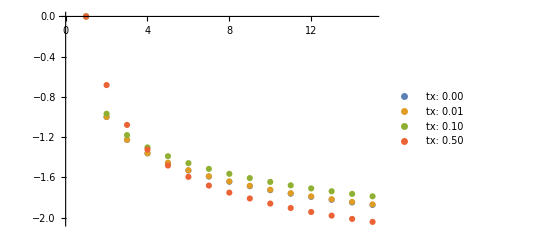

```mathematica
ListPlot[%, PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  txlist]]
```

## Lots of mess

```mathematica
Table[Total[Flatten[Take[integratedmntable, i,i]]],{i, Dimensions[integratedmntable][[1]]}]
```

{0,-1.06608,-1.36709,-1.56602,-1.72586,-1.86637,-1.99699,-2.12264,-2.24497,-2.36553,-2.48173}

```mathematica
integratedtxtable=NIntegrate[txtable/.tz->0, {kappa, -Infinity, Infinity}];
integratedtxtable[[;;,1,1]]=0;
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

```mathematica
Table[
Table[Total[Flatten[Take[integratedtxtable[[txindex]], i,i]]],{i, Dimensions[integratedmntable[[txindex]]][[1]]}],
{txindex, Length[integratedtxtable]}
]
```

{{0,0.5,0.613706,0.680915,0.72873,0.765859,0.796212,0.821884,0.844126,0.863747,0.881301},{0,0.499526,0.612911,0.679828,0.727377,0.764264,0.794392,0.819854,0.8419,0.861338,0.878718},{0,0.47544,0.579933,0.640165,0.683286,0.717236,0.745402,0.769515,0.790593,0.809297,0.826095},{0,0.23928,0.361914,0.433901,0.482114,0.518044,0.546539,0.57005,0.589941,0.607022,0.621847}}

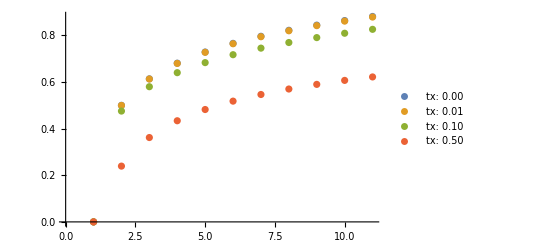

```mathematica
ListPlot[%, PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  txlist]]
```

```mathematica
NIntegrate[mntable/.tz->0/.tx->0.4, {kappa, -Infinity, Infinity}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
%//TableForm
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate[Indeterminate,{kappa,-∞,∞}] | -0.485013 | -0.0343274 | -0.00742481 | -0.00338072 | -0.00210374 | -0.00150703 | -0.00116621 | -0.000947211 | -0.000795186 | -0.000683741
0. | 0. | -0.0746418 | -0.0349171 | -0.0115599 | -0.00509221 | -0.00296299 | -0.002021 | -0.00150849 | -0.0011916 | -0.000978443
0. | 0.00246724 | 0. | -0.0245295 | -0.0296833 | -0.0144091 | -0.00677633 | -0.00383661 | -0.00253949 | -0.00185218 | -0.00143654
0. | 0.00169084 | 0.00383796 | 0. | -0.00784619 | -0.0218215 | -0.0155825 | -0.00832404 | -0.00473115 | -0.00306856 | -0.00219935
0. | 0.00126064 | 0.00254983 | 0.00477565 | 0. | -0.00243208 | -0.01402 | -0.0149938 | -0.00954445 | -0.00563404 | -0.00361601
0. | 0.0010026 | 0.00177851 | 0.00339239 | 0.00515562 | 0. | -0.00137424 | -0.007817 | -0.0129209 | -0.0102097 | -0.00649485
0. | 0.000830754 | 0.00134676 | 0.00230485 | 0.00416276 | 0.00495234 | 0. | -0.00168026 | -0.00380376 | -0.00994648 | -0.0101378
0. | 0.000708058 | 0.00107656 | 0.00169348 | 0.00284358 | 0.00476522 | 0.00426033 | 0. | -0.00202453 | -0.00183799 | -0.00679073
0. | 0.000616064 | 0.000892632 | 0.00132266 | 0.00204754 | 0.00338612 | 0.00508723 | 0.00327378 | 0. | -0.00197495 | -0.00132625
0. | 0.000544534 | 0.000759882 | 0.00107683 | 0.00157126 | 0.00241413 | 0.003901 | 0.00504046 | 0.00223109 | 0. | -0.00157402
0. | 0.000487326 | 0.000659841 | 0.000903068 | 0.00126186 | 0.00182517 | 0.00279596 | 0.00432927 | 0.00460276 | 0.00134535 | 0.

```mathematica
tx0values=MapThread[Flatten[{#1, #2}]&, {Flatten[%144], Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "tx0.csv"}], tx0values]
```

/home/thorvald/Documents/NTNU/09semester/ProjectThesis/Thesis/tx0.csv

```mathematica
tx01values=MapThread[Flatten[{#1, #2}]&, {Flatten[%166], Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "tx0.1.csv"}], tx01values]
```

/home/thorvald/Documents/NTNU/09semester/ProjectThesis/Thesis/tx0.1.csv

```mathematica
tx04values=MapThread[Flatten[{#1, #2}]&, {Flatten[%175], Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "tx0.4.csv"}], tx01values]
```

/home/thorvald/Documents/NTNU/09semester/ProjectThesis/Thesis/tx0.4.csv

```mathematica
Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]
```

{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},{0,-11},{0,-12},{1,-1},{1,-2},{1,-3},{1,-4},{1,-5},{1,-6},{1,-7},{1,-8},{1,-9},{1,-10},{1,-11},{1,-12},{2,-1},{2,-2},{2,-3},{2,-4},{2,-5},{2,-6},{2,-7},{2,-8},{2,-9},{2,-10},{2,-11},{2,-12},{3,-1},{3,-2},{3,-3},{3,-4},{3,-5},{3,-6},{3,-7},{3,-8},{3,-9},{3,-10},{3,-11},{3,-12},{4,-1},{4,-2},{4,-3},{4,-4},{4,-5},{4,-6},{4,-7},{4,-8},{4,-9},{4,-10},{4,-11},{4,-12},{5,-1},{5,-2},{5,-3},{5,-4},{5,-5},{5,-6},{5,-7},{5,-8},{5,-9},{5,-10},{5,-11},{5,-12},{6,-1},{6,-2},{6,-3},{6,-4},{6,-5},{6,-6},{6,-7},{6,-8},{6,-9},{6,-10},{6,-11},{6,-12},{7,-1},{7,-2},{7,-3},{7,-4},{7,-5},{7,-6},{7,-7},{7,-8},{7,-9},{7,-10},{7,-11},{7,-12},{8,-1},{8,-2},{8,-3},{8,-4},{8,-5},{8,-6},{8,-7},{8,-8},{8,-9},{8,-10},{8,-11},{8,-12},{9,-1},{9,-2},{9,-3},{9,-4},{9,-5},{9,-6},{9,-7},{9,-8},{9,-9},{9,-10},{9,-11},{9,-12},{10,-1},{10,-2},{10,-3},{10,-4},{10,-5},{10,-6},{10,-7},{10,-8},{10,-9},{10,-10},{10,-11},{10,-12}}

```mathematica
MatrixPlot[integratedmntable, PlotLegends->Automatic]
```

-Graphics-

```mathematica
MatrixPlot[Transpose[%], PlotLegends->Automatic]
```

-Graphics-

```mathematica
Table[Total[Flatten[Take[%111, i,i]]],{i, 11}]
```

{-0.499994,-0.613694,-0.680899,-0.728709,-0.765834,-0.796183,-0.821851,-0.844089,-0.863706,-0.881256,-0.897133}

```mathematica
Differences[%128]
```

{-0.1137,-0.0672045,-0.0478106,-0.0371247,-0.0303492,-0.0256675,-0.0222382,-0.0196178,-0.01755,-0.0158767}

```mathematica
MatrixPlot[Transpose[PadLeft[%23]], PlotLegends->Automatic]
```

-Graphics-

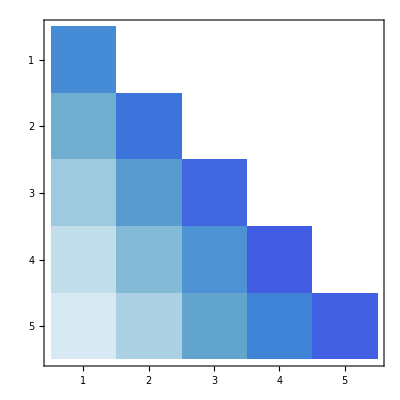

```mathematica
MatrixPlot[
Drop[
LowerTriangularize[Transpose[PadLeft[%23]], -1],
1, -2]
]
```

```mathematica
MatrixPlot[Transpose[PadRight[%86]], PlotLegends->Automatic]
```

-Graphics-

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

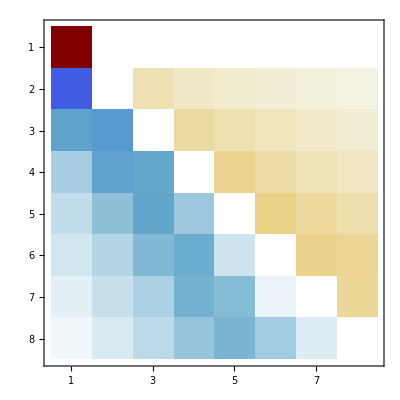

```mathematica
MatrixPlot[%]
```

```mathematica
%
```

{{0.0742869},{0.022533,0.0792403},{0.0112906,0.0278183,0.0703913},{0.00704959,0.013459,0.0312851,0.0549584},{0.00493117,0.00812744,0.0153973,0.0325317,0.0380931},{0.00369599,0.0055591,0.00911439,0.0171092,0.0312307,0.0235478},{0.00290218,0.00410079,0.00613415,0.0100596,0.0184352,0.0275079,0.0134442}}

```mathematica
MatrixPlot[%113, PlotLegends->Automatic]
```

-Graphics-

```mathematica
Total[%, {2}]Ξ2/.N->N-1, M->M-1)
```

{0.111009,0.0701791,0.0589379,0.0515723,0.0463516,0.0426362,0.0399899}

```mathematica
Ξ2/.N->N-1, M->M-1)
```

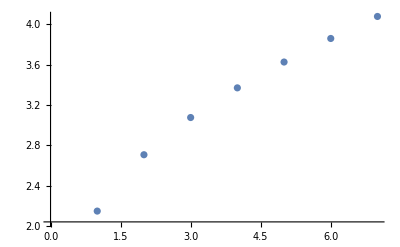

```mathematica
ListPlot[-Accumulate[%]*4]
```

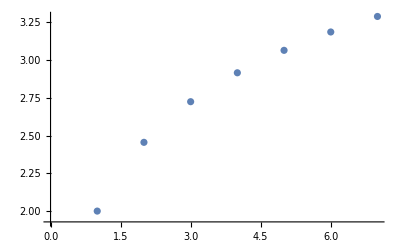

```mathematica
ListPlot[-Accumulate[%]*4]
```

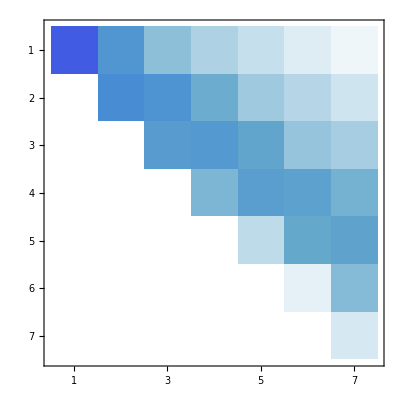

```mathematica
MatrixPlot[PadLeft[%]]
```

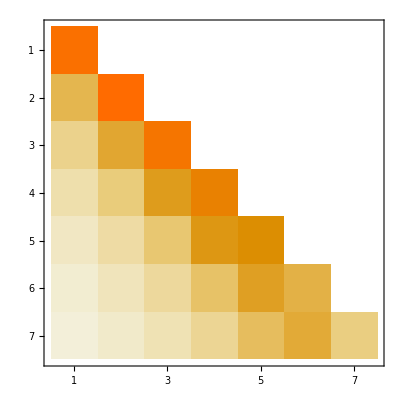

```mathematica
MatrixPlot[%]
```